```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jedli\OneDrive - NUS High School\Documents\Computing Studies\computed_tomography\logs

```mathematica
data=Import["random_masking_fine-tune_5_epochs.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
```

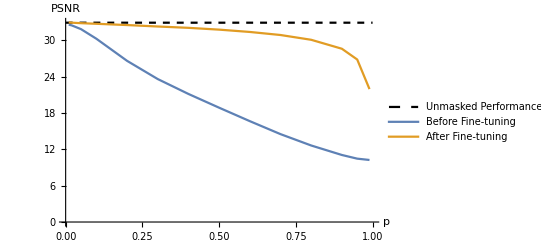

```mathematica
ListPlot[{{{0,data[[2]][[6]]},{1,data[[2]][[6]]}},Map[{#[[2]],#[[5]]}&,data],Map[{#[[2]],#[[6]]}&,data]},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.325,0.2}],Joined->True]
```

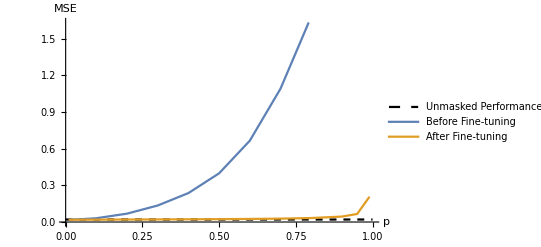

```mathematica
ListPlot[{{{0,data[[2]][[3]]},{1,data[[2]][[3]]}},Map[{#[[2]],#[[3]]}&,data],Map[{#[[2]],#[[4]]}&,data]},AxesLabel->{"p","MSE"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.325,0.8}],Joined->True]
```